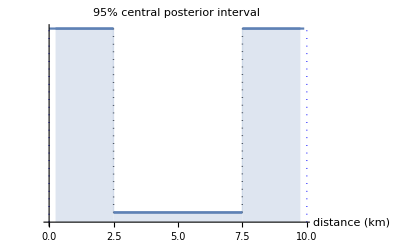

```mathematica
g1=Show[Plot[SquareWave[{0.2,0.01},((x-2.5)/10)],{x,0,9.9},ExclusionsStyle->{Dotted},Axes->{True,False},Ticks->{Automatic,None},BaseStyle->{FontSize->16},Epilog->{{Dotted,Blue,Line[{{0,0},{0,0.2}}]},{Dotted,Blue,Line[{{10,0},{10,0.2}}]}},PlotLabel->"95% central posterior interval",AxesLabel->{"distance (km)"}],Plot[SquareWave[{0.2,0.01},((x-2.5)/10)],{x,0.25,9.75},Filling->Axis]]
```

```mathematica
Integrate[SquareWave[{0.2,0},((x-2.5)/10)],{x,0,10}]
```

1.

```mathematica
Clear[α]
```

```mathematica
Solve[{Integrate[SquareWave[{0.2,0},((x-2.5)/10)],{x,0+α,10-α},Assumptions->0<α<1]==0.95,0≤ α≤ 1},α,Reals]
```

{{α→0.125}}

```mathematica
Integrate[SquareWave[{0.2,0.01},((x-2.5)/10)],{x,2.5,7.5}]
```

0.05

```mathematica
Integrate[SquareWave[{0.2,0.01},((x-2.5)/10)],{x,0.25,9.75}]
```

0.95

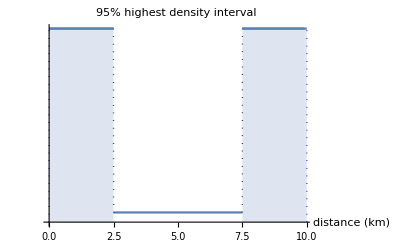

```mathematica
g2=Show[Plot[SquareWave[{0.2,0.01},((x-2.5)/10)],{x,0,9.9},ExclusionsStyle->{Dotted},Axes->{True,False},Ticks->{Automatic,None},BaseStyle->{FontSize->16},Epilog->{{Dotted,Blue,Line[{{0,0},{0,0.2}}]},{Dotted,Blue,Line[{{10,0},{10,0.2}}]}},PlotLabel->"95% highest density interval",AxesLabel->{"distance (km)"}],Plot[SquareWave[{0.2,0.01},((x-2.5)/10)],{x,0,2.5},Filling->Axis],Plot[SquareWave[{0.2,0.01},((x-2.5)/10)],{x,7.5,10},Filling->Axis]]
```

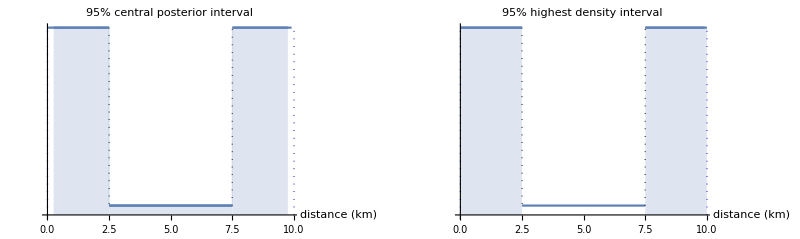

```mathematica
Show[GraphicsRow[{g1,g2}],ImageSize->800]
```